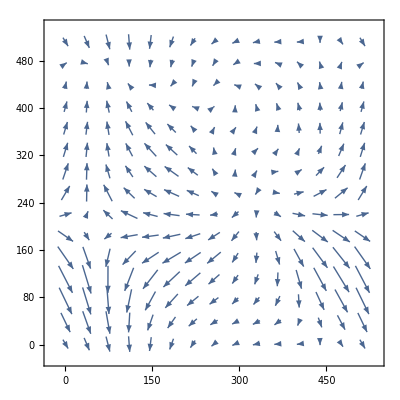

DiscreteWaveletData[<<DWT>>, <3>, {512, 512}]

DiscreteWaveletData[<<DWT>>, <3>, {512, 512}]

List

-Graphics-

```mathematica
v=Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\velocity.txt","Table"];
u=Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\uelocity.txt","Table"];
t = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\t.txt","Table"];
ListVectorPlot[Table[{u[[x,y]],v[[x,y]]},{x,512},{y,512}]]
dwdu = DiscreteWaveletTransform[u,ReverseBiorthogonalSplineWavelet[1,3],3]
dwdv = DiscreteWaveletTransform[u,ReverseBiorthogonalSplineWavelet[1,3],3]
Normal[dwdv][[0]]
```